# Heat stress and bleaching in corals: a bioenergetic model

## Pfab et al, 2024 ferdinand.pfab@gmail.com Code for time series

```mathematica
Get[NotebookDirectory[]<>#]&/@{
(*load model definition*)
"23_10_04_simulation_1.m",
(*load parameter values*)
"23_10_04_parameters_1.m",
(*load functions and options for simulations and plots*)
"23_10_04_styles_1.m"
};
```

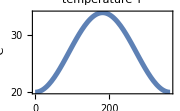

```mathematica
(*define the seasonal environment*)
sinusmin=20;
sinusmax=34;
sinusmax2=30;
Trange={T->{sinusmin-2,sinusmax+2}};
makesinusenvironment[min_,max_]:={T->Piecewise[{{min+(max-min)/2+(max-min)/2 Sin[3/2  π+(2 π)/365. t], True}, {0, True}}]};
environment=makesinusenvironment[sinusmin,sinusmax];
partplot[T,Join[environment,parvalsFvFmArr],{},{PlotRange->Automatic,AxesOrigin->Automatic}]
```

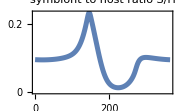

```mathematica
(*run a simulation of the model with this environment, plot symbiont host ratio S/H*)
sol=simulate[Join[parvalsFvFmArr,environment],fluxvars,inivalsdefault/.parvalsFvFmArr/.T->28];
partplot[S/H,Join[parvalsFvFmArr,environment],sol,{}]
```

```mathematica
(*now do all the plots for the paper*)
```

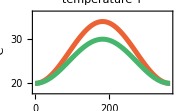
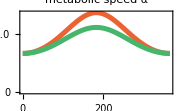
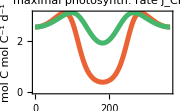
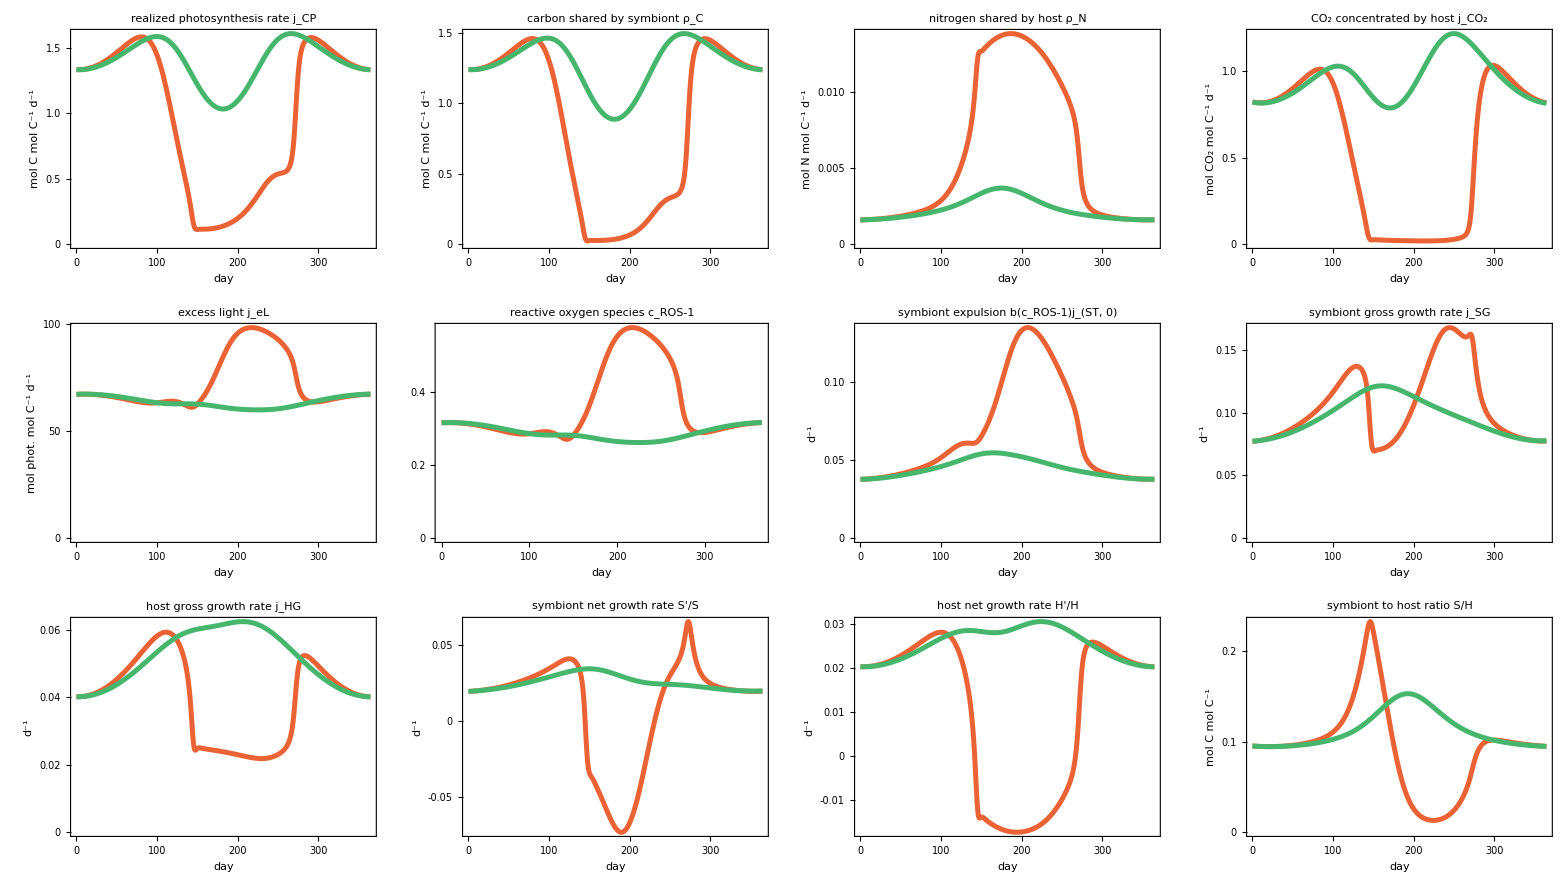
-Graphics-peak temperature
-Graphics- | 34°C
-Graphics- | 30°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

```mathematica
(*Fig 3*)
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-FvFm-Arr-2-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsFvFmArr,makesinusenvironment[sinusmin,#]]&/@{sinusmax,sinusmax2},Evaluate@colorsmultsimus,inivalsdefault,Trange]
```

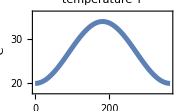
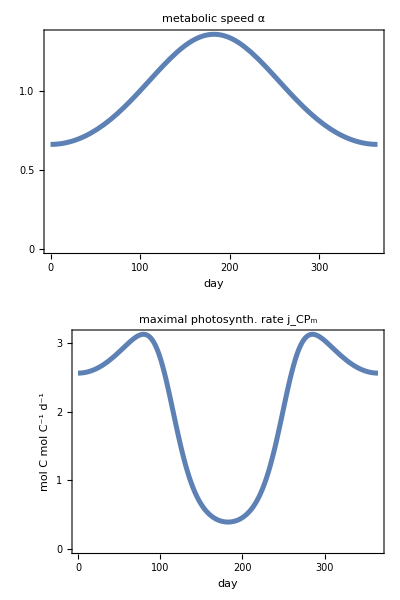
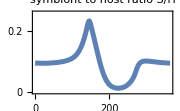
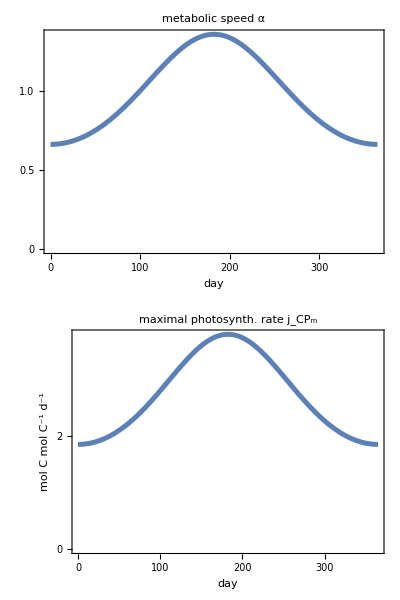
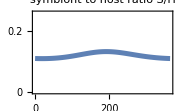
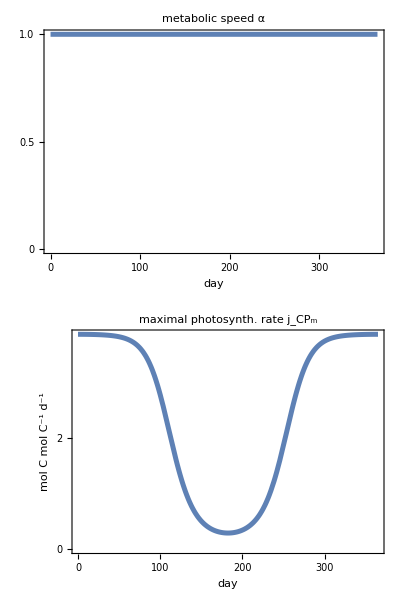
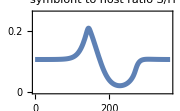
-Graphics- | -Graphics-
-Graphics- | -Graphics-
    
full model

-Graphics-
-Graphics-
-Graphics-
acceleration model

-Graphics-
-Graphics-
-Graphics-
damage model

-Graphics-
-Graphics-
-Graphics-

```mathematica
(*Fig. 4*)
(Export[NotebookDirectory[]<>"export/"<>"simus-Short-All.pdf",#];#)&@Column[{Grid[{{arrow2,Column[{Framed[Column[{partplot[T,Join[makesinusenvironment[sinusmin,sinusmax],parvalsFvFmArr],{},{PlotRange->T/.Trange,AxesOrigin->Automatic}]}],RoundingRadius->framingRadius],arrow1},Alignment->Center],arrow3}},Alignment->Bottom],
Row[(PanelPlotShort@@#)&/@{
{Join[parvalsFvFmArr,makesinusenvironment[sinusmin,sinusmax]],"full model"},
{Join[parvalsArr,makesinusenvironment[sinusmin,sinusmax]],"acceleration model"},
{Join[parvalsFvFm,makesinusenvironment[sinusmin,sinusmax]],"damage model"}
}, "  "]},Alignment->Center,Spacings->0]
```

```mathematica
(*Fig. S1*)
PWplot["simus-sinus-FvFm-Arr.pdf",Join[parvalsFvFmArr,makesinusenvironment[sinusmin,sinusmax]],Join[{H->#,S->.2#}&@(200{.005,1}),Trange,SUmaxs]]
PWplot["simus-sinus-FvFm.pdf",Join[parvalsFvFm,makesinusenvironment[sinusmin,sinusmax]],Join[{H->#,S->.2#}&@(1{1,1000}),Trange,SUmaxs]]
PWplot["simus-sinus-Arr.pdf",Join[parvalsArr,makesinusenvironment[sinusmin,sinusmax]],Join[{H->#,S->.2#}&@(100{10,10^5}),Trange,SUmaxs]]
```

```mathematica
(*Fig. S2*)
PWplot["simus-sinus-2-FvFm-Arr.pdf",Join[parvalsFvFmArr,makesinusenvironment[sinusmin,sinusmax2]],Join[{H->#,S->.2#}&@(10^7{.00005,1}),Trange,SUmaxs]]
PWplot["simus-sinus-2-FvFm.pdf",Join[parvalsFvFm,makesinusenvironment[sinusmin,sinusmax2]],Join[{H->#,S->.2#}&@(10^7{.00005,1}),Trange,SUmaxs]]
PWplot["simus-sinus-2-Arr.pdf",Join[parvalsArr,makesinusenvironment[sinusmin,sinusmax2]],Join[{H->#,S->.2#}&@(10^7{.00005,1}),Trange,SUmaxs]]
```

```mathematica
(*Fig. S8*)
Trangepw={T->{18,37}};
environmentpw={T->20+14(1-sigmoidFunction /.{ED50->25,steepness->.2,T->t,sigmax->1})};
PWplot["simus-pw-FvFm-Arr.pdf",Join[parvalsFvFmArr/.(tmax->_)->(tmax->100),environmentpw],Join[{H-> #,S-> .2# }&@({.5,50}),Trangepw,SUmaxs]]
PWplot["simus-pw-high-S-H-FvFm-Arr.pdf",Join[parvalsFvFmArr/.{(L->_)->(L->10),(tmax->_)->(tmax->100)},environmentpw],Join[{H-> #,S-> .2# }&@({1,100}),Trangepw,SUmaxs]]
```

```mathematica
(*Fig S4*)
PWplot["simus-sinus-unlimited-CO2-FvFm-Arr.pdf",Join[parvalsFvFmArr/.ReplacePars[{kCO2->10^6}],makesinusenvironment[sinusmin,sinusmax]],Join[{H->#,S->.2#}&@(200{.005,1}),Trange,SUmaxs]]
PWplot["simus-sinus-unlimited-CO2-FvFm.pdf",Join[parvalsFvFm/.ReplacePars[{kCO2->10^6}],makesinusenvironment[sinusmin,sinusmax]],Join[{H->#,S->.2#}&@(200{.005,1}),Trange,SUmaxs]]
PWplot["simus-sinus-unlimited-CO2-Arr.pdf",Join[parvalsArr/.ReplacePars[{kCO2->10^6}],makesinusenvironment[sinusmin,sinusmax]],Join[{H->#,S->.2#}&@(200{.005,1}),Trange,SUmaxs]]
```

```mathematica
(*Fig. S3*)
numbertempruns=7;
sinusenvironments=Table[makesinusenvironment[sinusmin,27(*30.5*)+ i],{i,numbertempruns}];
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-FvFm-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsFvFmArr,#]&/@sinusenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numbertempruns-1)]},{i,numbertempruns}]},inivalsdefault,Trange]
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-FvFm-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsFvFm,#]&/@sinusenvironments ,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numbertempruns-1)]},{i,numbertempruns}]},inivalsdefault,Trange]
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsArr,#]&/@sinusenvironments ,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numbertempruns-1)]},{i,numbertempruns}]},inivalsdefault,Trange]
```

```mathematica
(*Fig. S9*)
environmentup[minT_,maxT_]:={T->minT+(maxT-minT)(1-sigmoidFunction /.{ED50->10.5,steepness->2,T->t,sigmax->1})};
numberupruns=5;
upenvironments=Table[environmentup[24,26+2i],{i,numberupruns}];
uptimes=((tmax->_)->(tmax->60));
Trangeup={T->{22,42}};
(Export[NotebookDirectory[]<>"export/"<>"simus-up-FvFm-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsFvFmArr/.uptimes,#]&/@upenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numberupruns-1)]},{i,numberupruns}]},inivalsdefault,Trangeup]
(Export[NotebookDirectory[]<>"export/"<>"simus-up-FvFm-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsFvFm/.uptimes,#]&/@upenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numberupruns-1)]},{i,numberupruns}]},inivalsdefault,Trangeup]
(Export[NotebookDirectory[]<>"export/"<>"simus-up-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot1,toplot2,Join[parvalsArr/.uptimes,#]&/@upenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numberupruns-1)]},{i,numberupruns}]},inivalsdefault,Trangeup]
```

```mathematica
(*Fig. S6*)
increase[txs_]:=Piecewise[Join[Table[{txs[[i,2]]+(txs[[i+1,2]]-txs[[i,2]])((t-txs[[i,1]])/(txs[[i+1,1]]-txs[[i,1]])),t<txs[[i+1,1]]},{i,1,Length[txs]-1}],{{txs[[-1,2]],True}}]];
TrangeUpDown={T->{20,38}};
updowntimes={30,60};
updownmin=26;
updownmax=34;
environmentupdown={T->increase[{{"NA",updownmin},{updowntimes[[1]],updownmin},{updowntimes[[1]]+1.5,updownmax},{updowntimes[[2]]-1.5,updownmax},{updowntimes[[2]],updownmin}}]};
PWplot["simus-updown-no-hysteresis-FvFm-Arr.pdf",Join[parvalsFvFmArr/.(tmax->_)->(tmax->130),environmentupdown],Join[{H->#,S->.2#}&@(4{.1,10}),TrangeUpDown,SUmaxs]]
PWplot["simus-updown-hysteresis-FvFm-Arr.pdf",Join[parvalsFvFmArr/.{(X->_)->(X->7.5 10^-8),(tmax->_)->(tmax->130)},environmentupdown],Join[{H->#,S->.2#}&@({.01,10}),TrangeUpDown,SUmaxs]]
```

```mathematica
(*Fig S7*)
environmentupdownShort={T->increase[{{"NA",updownmin},{updowntimes[[1]],updownmin},{updowntimes[[1]]+1,updownmax},{updowntimes[[1]]+4,updownmax},{updowntimes[[1]]+5,updownmin}}]};
PWplot["simus-updown-hysteresis-short-FvFm-Arr.pdf",Join[parvalsFvFmArr/.{(X->_)->(X->7.5 10^-8),(tmax->_)->(tmax->130)},environmentupdownShort],Join[{H->#,S->.2#}&@({.01,10}),TrangeUpDown,SUmaxs]]
```

```mathematica
(*Fig. S10*)
(Export[NotebookDirectory[]<>"export/"<>"simus-intervention-X.pdf",#];#)&@PanelPlotMultipleParameters[{T,10^6 X},toplot2,Join[makesinusenvironment[sinusmin,sinusmax],#]&/@{parvalsFvFmArr,(parvalsFvFmArr/.{(X->_)->(X->(Piecewise[{{3, 365/2-6 7<t<365/2+6 7}, {1, True}}](X/.parvalsFvFmArr)))})},inivalsdefault,Join[{H->#,S->.2#}&@(200{.005,1}),Trange]]
(Export[NotebookDirectory[]<>"export/"<>"simus-intervention-L.pdf",#];#)&@PanelPlotMultipleParameters[{T,L},toplot2,Join[makesinusenvironment[sinusmin,sinusmax],#]&/@{parvalsFvFmArr,(parvalsFvFmArr/.{(L->_)->(L->(Piecewise[{{.8, 365/2-6 7<t<365/2+6 7}, {1, True}}](L/.parvalsFvFmArr)))})},inivalsdefault,Join[{H->#,S->.2#}&@(200{.005,1}),Trange]]
(Export[NotebookDirectory[]<>"export/"<>"simus-intervention-N.pdf",#];#)&@PanelPlotMultipleParameters[{T,10^6 Ν},toplot2,Join[makesinusenvironment[sinusmin,sinusmax],#]&/@{parvalsFvFmArr,(parvalsFvFmArr/.{(Ν->_)->(Ν->(Piecewise[{{0, 365/2-6 7<t<365/2+6 7}, {1, True}}](Ν/.parvalsFvFmArr)))})},inivalsdefault,Join[{H->#,S->.2#}&@(200{.005,1}),Trange]]
```